## Load Metrics package

```mathematica
<<Metrics`LoadMetric`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.1.2, {2011,7,15}

CopyRight (C) 2003-2011, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.0.2, {2011,7,15}

CopyRight (C) 2002-2011, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.7.2, {2011,7,15}

CopyRight (C) 2005-2011, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
$DefInfoQ=False;
$CVVerbose=False;
$UndefInfoQ=False;
```

## Minkowski

```mathematica
LoadMetric["Minkowski"]
```

```mathematica
MetricCompute[g,Minkowski,"Einstein"[-1,-1],CVSimplify->Simplify];
```

Metric[1,1] constructed in 0.1904 seconds

Applied Simplify in 0.03012 seconds

Stored in 0.000867 seconds and 6152 bytes

DMetric[-1,-1,-1] constructed in 0.004653 seconds

Applied Simplify in 0.00115 seconds

Stored in 0.00179 seconds and 53064 bytes

Christoffel[-1,-1,-1] constructed in 0.000571 seconds

Applied Simplify in 0.00114 seconds

Stored in 0.00255 seconds and 65704 bytes

Christoffel[1,-1,-1] constructed in 0.02534 seconds

Applied Simplify in 0.0013 seconds

Stored in 0.00328 seconds and 57064 bytes

DDMetric[-1,-1,-1,-1] constructed in 0.0013 seconds

Applied Simplify in 0.004826 seconds

Stored in 0.00918 seconds and 312264 bytes

Riemann[-1,-1,-1,-1] constructed in 0.008243 seconds

Applied Simplify in 0.00064 seconds

Stored in 0.01837 seconds and 295320 bytes

Riemann[-1,-1,-1,1] constructed in 0.003931 seconds

Applied Simplify in 0.005972 seconds

Stored in 0.01733 seconds and 250504 bytes

Ricci[-1,-1] constructed in 0.00026 seconds

Applied Simplify in 0.00034 seconds

Stored in 0.000602 seconds and 9672 bytes

RicciScalar[] constructed in 0.000095 seconds

Applied Simplify in 0.000054 seconds

Stored in 0.00012 seconds and 264 bytes

Einstein[-1,-1] constructed in 0.00019 seconds

Applied Simplify in 0.000385 seconds

Stored in 0.000541 seconds and 9672 bytes

```mathematica
ComponentArray[EinsteinCD[-a,-b]//ToBasis[Minkowski]]/.TensorValues[EinsteinCD]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
UnloadMetric[]
```

## Gauge wave

```mathematica
LoadMetric["GaugeWave"]
```

```mathematica
MetricCompute[g,GaugeWave,"Einstein"[-1,-1],CVSimplify->Simplify];
```

Metric[1,1] constructed in 0.21602 seconds

Applied Simplify in 0.13104 seconds

Stored in 0.000908 seconds and 7448 bytes

DMetric[-1,-1,-1] constructed in 0.00081 seconds

Applied Simplify in 0.02991 seconds

Stored in 0.00197 seconds and 55464 bytes

Christoffel[-1,-1,-1] constructed in 0.00073 seconds

Applied Simplify in 0.02707 seconds

Stored in 0.00228 seconds and 70376 bytes

Christoffel[1,-1,-1] constructed in 0.00125 seconds

Applied Simplify in 0.09247 seconds

Stored in 0.00257 seconds and 67008 bytes

DDMetric[-1,-1,-1,-1] constructed in 0.00166 seconds

Applied Simplify in 0.04661 seconds

Stored in 0.009287 seconds and 316344 bytes

Riemann[-1,-1,-1,-1] constructed in 0.00209 seconds

Applied Simplify in 0.000637 seconds

Stored in 0.01806 seconds and 295320 bytes

Riemann[-1,-1,-1,1] constructed in 0.004465 seconds

Applied Simplify in 0.006553 seconds

Stored in 0.01735 seconds and 250504 bytes

Ricci[-1,-1] constructed in 0.00026 seconds

Applied Simplify in 0.00033 seconds

Stored in 0.000634 seconds and 9672 bytes

RicciScalar[] constructed in 0.00012 seconds

Applied Simplify in 0.000063 seconds

Stored in 0.000578 seconds and 264 bytes

Einstein[-1,-1] constructed in 0.00022 seconds

Applied Simplify in 0.00034 seconds

Stored in 0.00052 seconds and 9672 bytes

```mathematica
RuleToSet[EinsteinCD]
```

```mathematica
ComponentArray[EinsteinCD[-a,-b]//ToBasis[GaugeWave]]/.TensorValues[EinsteinCD]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
UnloadMetric[]
```

## Shifted gauge wave

```mathematica
LoadMetric["ShiftedGaugeWave"]
```

```mathematica
MetricCompute[g,ShiftedGaugeWave,"Einstein"[-1,-1],CVSimplify->Simplify];
```

Metric[1,1] constructed in 0.00124 seconds

Applied Simplify in 0.02582 seconds

Stored in 0.000891 seconds and 7824 bytes

DMetric[-1,-1,-1] constructed in 0.000883 seconds

Applied Simplify in 0.02675 seconds

Stored in 0.00185 seconds and 56664 bytes

Christoffel[-1,-1,-1] constructed in 0.000895 seconds

Applied Simplify in 0.0257 seconds

Stored in 0.00219 seconds and 70376 bytes

Christoffel[1,-1,-1] constructed in 0.00149 seconds

Applied Simplify in 0.02008 seconds

Stored in 0.00227 seconds and 65352 bytes

DDMetric[-1,-1,-1,-1] constructed in 0.00306 seconds

Applied Simplify in 0.02789 seconds

Stored in 0.007852 seconds and 318384 bytes

Riemann[-1,-1,-1,-1] constructed in 0.00168 seconds

Applied Simplify in 0.0017 seconds

Stored in 0.01674 seconds and 295320 bytes

Riemann[-1,-1,-1,1] constructed in 0.004596 seconds

Applied Simplify in 0.006121 seconds

Stored in 0.01744 seconds and 250504 bytes

Ricci[-1,-1] constructed in 0.0003 seconds

Applied Simplify in 0.00034 seconds

Stored in 0.000604 seconds and 9672 bytes

RicciScalar[] constructed in 0.00013 seconds

Applied Simplify in 0.000058 seconds

Stored in 0.00017 seconds and 264 bytes

Einstein[-1,-1] constructed in 0.00021 seconds

Applied Simplify in 0.00032 seconds

Stored in 0.000506 seconds and 9672 bytes

```mathematica
ComponentArray[EinsteinCD[-a,-b]//ToBasis[ShiftedGaugeWave]]/.TensorValues[EinsteinCD]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
UnloadMetric[]
```

## Kerr-Schild

```mathematica
LoadMetric["KerrSchild"]
```

```mathematica
SimplifyWithR[expr_]:=Module[{expr2},
expr2=expr/.{Derivative[1,0,0][r][x[],y[],z[]]->(r[x[],y[],z[]]x[])/(a^2+2 r[x[],y[],z[]]^2-x[]^2-y[]^2-z[]^2),Derivative[0,1,0][r][x[],y[],z[]]->(r[x[],y[],z[]]y[])/(a^2+2 r[x[],y[],z[]]^2-x[]^2-y[]^2-z[]^2),Derivative[0,0,1][r][x[],y[],z[]]->-(((a^2+r[x[],y[],z[]]^2)*z[])/(r[x[],y[],z[]]*(-a^2-2*r[x[],y[],z[]]^2+x[]^2+y[]^2+z[]^2))),Derivative[2,0,0][r][x[],y[],z[]]->(r[x[],y[],z[]]*(4*r[x[],y[],z[]]^2*x[]^2+3*x[]^2*(-a^2-2*r[x[],y[],z[]]^2+x[]^2+y[]^2+z[]^2)-(-a^2-2*r[x[],y[],z[]]^2+x[]^2+y[]^2+z[]^2)^2))/(-a^2-2*r[x[],y[],z[]]^2+x[]^2+y[]^2+z[]^2)^3,Derivative[0,2,0][r][x[],y[],z[]]->(r[x[],y[],z[]]*(4*r[x[],y[],z[]]^2*y[]^2+3*y[]^2*(-a^2-2*r[x[],y[],z[]]^2+x[]^2+y[]^2+z[]^2)-(-a^2-2*r[x[],y[],z[]]^2+x[]^2+y[]^2+z[]^2)^2))/(-a^2-2*r[x[],y[],z[]]^2+x[]^2+y[]^2+z[]^2)^3,Derivative[0,0,2][r][x[],y[],z[]]->-(((a^2+r[x[],y[],z[]]^2)*(r[x[],y[],z[]]^2*(-a^2-2*r[x[],y[],z[]]^2+x[]^2+y[]^2)^2-(a^4+a^2*(5*r[x[],y[],z[]]^2-x[]^2-y[]^2)+r[x[],y[],z[]]^2*(2*r[x[],y[],z[]]^2+x[]^2+y[]^2))*z[]^2+(a^2-2*r[x[],y[],z[]]^2)*z[]^4))/(r[x[],y[],z[]]^3*(-a^2-2*r[x[],y[],z[]]^2+x[]^2+y[]^2+z[]^2)^3)),Derivative[1,1,0][r][x[],y[],z[]]->-((r[x[],y[],z[]]*x[]*y[]*(3*a^2+2*r[x[],y[],z[]]^2-3*(x[]^2+y[]^2+z[]^2)))/(-a^2-2*r[x[],y[],z[]]^2+x[]^2+y[]^2+z[]^2)^3),Derivative[1,0,1][r][x[],y[],z[]]->(x[]*z[]*(-a^4+a^2*(-r[x[],y[],z[]]^2+x[]^2+y[]^2+z[]^2)+r[x[],y[],z[]]^2*(-2*r[x[],y[],z[]]^2+3*(x[]^2+y[]^2+z[]^2))))/(r[x[],y[],z[]]*(-a^2-2*r[x[],y[],z[]]^2+x[]^2+y[]^2+z[]^2)^3),Derivative[0,1,1][r][x[],y[],z[]]->(y[]*z[]*(-a^4+a^2*(-r[x[],y[],z[]]^2+x[]^2+y[]^2+z[]^2)+r[x[],y[],z[]]^2*(-2*r[x[],y[],z[]]^2+3*(x[]^2+y[]^2+z[]^2))))/(r[x[],y[],z[]]*(-a^2-2*r[x[],y[],z[]]^2+x[]^2+y[]^2+z[]^2)^3)};
expr2
]
```

```mathematica
MetricCompute[g,KerrSchild,"Einstein"[-1,-1],CVSimplify->SimplifyWithR];
```

Metric[1,1] constructed in 0.048958 seconds

Applied SimplifyWithR in 0.00671 seconds

Stored in 0.00174 seconds and 146848 bytes

DMetric[-1,-1,-1] constructed in 0.00121 seconds

Applied SimplifyWithR in 0.02274 seconds

Stored in 0.00275 seconds and 390000 bytes

Christoffel[-1,-1,-1] constructed in 0.004453 seconds

Applied SimplifyWithR in 0.0258 seconds

Stored in 0.003852 seconds and 974352 bytes

Christoffel[1,-1,-1] constructed in 0.01181 seconds

Applied SimplifyWithR in 0.11167 seconds

Stored in 0.03285 seconds and 6761032 bytes

DDMetric[-1,-1,-1,-1] constructed in 0.03519 seconds

Applied SimplifyWithR in 0.13292 seconds

Stored in 0.01756 seconds and 4193920 bytes

Riemann[-1,-1,-1,-1] constructed in 0.01682 seconds

Applied SimplifyWithR in 0.415032 seconds

Stored in 0.02368 seconds and 21900600 bytes

Riemann[-1,-1,-1,1] constructed in 0.541249 seconds

Applied SimplifyWithR in 5.491238 seconds

Stored in 0.03343 seconds and 299474984 bytes

Ricci[-1,-1] constructed in 0.19217 seconds

Applied SimplifyWithR in 1.56261 seconds

Stored in 0.02881 seconds and 85809720 bytes

RicciScalar[] constructed in 0.007927 seconds

Applied SimplifyWithR in 1.54507 seconds

Stored in 0.27251 seconds and 85941824 bytes

Einstein[-1,-1] constructed in 1.45401 seconds

Applied SimplifyWithR in 16.84993 seconds

Stored in 0.28985 seconds and 945244256 bytes

```mathematica
simprule=(r[x,y,z]^4-a^2 z^2+r[x,y,z]^2 (a^2-x^2-y^2-z^2))->Simplify[(r[x,y,z]^4-a^2 z^2+r[x,y,z]^2 (a^2-x^2-y^2-z^2))/.{r[__]->Sqrt[(x^2+y^2+z^2-a^2+Sqrt[(x^2+y^2+z^2-a^2)^2+4 a^2 z^2])/2],x[]->x,y[]->y,z[]->z}]
```

r[x,y,z]^4-a^2 z^2+r[x,y,z]^2 (a^2-x^2-y^2-z^2)→0

In this case, we just check that the Ricci tensor is 0 for simplicity

```mathematica
Simplify[(ComponentArray[RicciCD[-b,-c]//ToBasis[KerrSchild]]/.TensorValues[RicciCD])]/.simprule
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

## Vaidya

```mathematica
LoadMetric["Vaidya"]
```

```mathematica
SimplifyWithR[expr_]:=Module[{expr2},
expr2=expr/.{Derivative[1,0,0][r][x[],y[],z[]]->x[]/r[x[],y[],z[]],Derivative[0,1,0][r][x[],y[],z[]]->y[]/r[x[],y[],z[]],Derivative[0,0,1][r][x[],y[],z[]]->z[]/r[x[],y[],z[]],Derivative[2,0,0][r][x[],y[],z[]]->(r[x[],y[],z[]]^2-x[]^2)/r[x[],y[],z[]]^3,Derivative[0,2,0][r][x[],y[],z[]]->(r[x[],y[],z[]]^2-y[]^2)/r[x[],y[],z[]]^3,Derivative[0,0,2][r][x[],y[],z[]]->((-2*r[x[],y[],z[]]^2+x[]^2+y[]^2)^2-(2*r[x[],y[],z[]]^2+x[]^2+y[]^2)*z[]^2-2*z[]^4)/r[x[],y[],z[]]^5,Derivative[1,1,0][r][x[],y[],z[]]->-((x[]*y[])/r[x[],y[],z[]]^3),Derivative[1,0,1][r][x[],y[],z[]]->-((x[]*z[])/r[x[],y[],z[]]^3),Derivative[0,1,1][r][x[],y[],z[]]->-((y[]*z[])/r[x[],y[],z[]]^3)};
expr2
]
```

```mathematica
MetricCompute[g,Vaidya,"Einstein"[-1,-1],CVSimplify->SimplifyWithR];
```

Metric[1,1] constructed in 0.05659 seconds

Applied SimplifyWithR in 0.003706 seconds

Stored in 0.00166 seconds and 130248 bytes

DMetric[-1,-1,-1] constructed in 0.004277 seconds

Applied SimplifyWithR in 0.01158 seconds

Stored in 0.00242 seconds and 206600 bytes

Christoffel[-1,-1,-1] constructed in 0.004259 seconds

Applied SimplifyWithR in 0.01044 seconds

Stored in 0.00261 seconds and 351064 bytes

Christoffel[1,-1,-1] constructed in 0.01133 seconds

Applied SimplifyWithR in 0.054925 seconds

Stored in 0.00452 seconds and 4013000 bytes

DDMetric[-1,-1,-1,-1] constructed in 0.02363 seconds

Applied SimplifyWithR in 0.060669 seconds

Stored in 0.008482 seconds and 1399616 bytes

Riemann[-1,-1,-1,-1] constructed in 0.045822 seconds

Applied SimplifyWithR in 0.20504 seconds

Stored in 0.02286 seconds and 12421720 bytes

Riemann[-1,-1,-1,1] constructed in 0.31233 seconds

Applied SimplifyWithR in 2.85008 seconds

Stored in 0.02706 seconds and 167638216 bytes

Ricci[-1,-1] constructed in 0.10516 seconds

Applied SimplifyWithR in 0.797056 seconds

Stored in 0.01263 seconds and 48012832 bytes

RicciScalar[] constructed in 0.000393 seconds

Applied SimplifyWithR in 0.850355 seconds

Stored in 0.15043 seconds and 48128368 bytes

Einstein[-1,-1] constructed in 0.15306 seconds

Applied SimplifyWithR in 9.307166 seconds

Stored in 0.31486 seconds and 529311016 bytes

```mathematica
Simplify[(ComponentArray[RicciCD[-b,-c]//ToBasis[Vaidya]]/.TensorValues[RicciCD]),Assumptions->r[x[],y[],z[]]==Sqrt[x[]^2+y[]^2+z[]^2]&&r[x[],y[],z[]]>0]
```

```mathematica
ricci=%/.Sqrt[x[]^2+y[]^2+z[]^2]->r[x[],y[],z[]];
```

For dM->0, we should have Schwarzschild (i.e. vacuum)

```mathematica
Flatten[ricci/.{dM->0}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
riccix=Simplify[ricci/.{r[__]->x[],y[]->0,z[]->0}]
```

{{(4 dM Sech[(dM (t+x))/M]^2 Tanh[(dM (t+x))/M])/x^2,1/(2 x^4)dM Sech[(dM (t+x))/M]^6 (Sinh[(4 dM (t+x))/M] (2 M x+x^2-2 M √(x^2))+2 x (2 dM x+Sinh[(2 dM (t+x))/M] x-2 dM √(x^2)+8 dM Cosh[(2 dM (t+x))/M] (-x+√(x^2))-2 dM Cosh[(4 dM (t+x))/M] (-x+√(x^2)))),0,0},{1/(2 x^4)dM Sech[(dM (t+x))/M]^6 (Sinh[(4 dM (t+x))/M] (2 M x+x^2-2 M √(x^2))+2 x (2 dM x+Sinh[(2 dM (t+x))/M] x-2 dM √(x^2)+8 dM Cosh[(2 dM (t+x))/M] (-x+√(x^2))-2 dM Cosh[(4 dM (t+x))/M] (-x+√(x^2)))),(4 dM Sech[(dM (t+x))/M]^2 Tanh[(dM (t+x))/M])/x^2,0,0},{0,0,0,0},{0,0,0,0}}

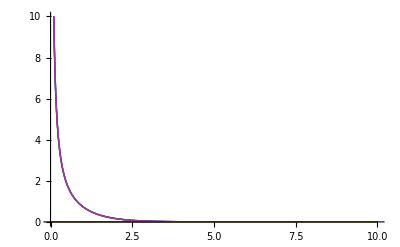

```mathematica
Plot[Evaluate[Flatten[Simplify[riccix/.{M->1,t[]->0,dM->1/2,x[]->xx}]]],{xx,0,10},PlotRange->{0,10}]
```